PDF of the supremum of Cauchy process X_t. f(x)= P(sup_(t≤ 1) X_t ϵ dx). ”The Maximum of Sums of Stable Random Variables”  D. A. Darling (1955)

```mathematica
f[x_]:=1/(π √x(1+x^2)^(3/4))Exp[-1/π NIntegrate[Log[w]/(1 + w^2),{w,0,x}]]
```

Survival probability

```mathematica
F[x_]:=NIntegrate[f[s],{s,0,x}]
```

```mathematica
(1-F[3])^2
```

NIntegrate::nlim: w = s is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

0.0140308

```mathematica
(1-F[11])^2
```

NIntegrate::nlim: w = s is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

0.00093398

The -3 truncation error for BM yields an error of 1.82222×10^-6. To get an equivalent error for the Cauchy process, we need a lower boundary truncation of 250. That is huge.

```mathematica
(1-F[250])^2
```

NIntegrate::nlim: w = s is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

1.63569×10^-6

```mathematica
(1-CDF[NormalDistribution[0,1],3])^2//N
```

1.82222×10^-6

```mathematica
Plot3D[PDF[CauchyDistribution[0,t],x],{t,0,1},{x,-3,3}, PlotRange-> {{0,1},{-3,3},{0,2}}]
```

-Graphics3D-

```mathematica
p[s_,t_,x_,y_]:= (t-s)/(π ((t-s)^2+(y-x)^2))
```

Transition density of a Cauchy process

```mathematica
phat[s_,t_,x_,y_,T_,z_]:=p[s,t,x,y] p[t,T,y,z]/p[s,T,x,z]//Simplify
```

```mathematica
phat[s,t,x,y,T,z]
```

((-s+t) (-t+T) ((s-T)^2+(x-z)^2))/(π (-s+T) ((s-t)^2+(x-y)^2) ((t-T)^2+(y-z)^2))

```mathematica
phat[0,t,0,y,1,0]
```

-((-1+t) t)/(π (t^2+y^2) (1-2 t+t^2+y^2))

```mathematica
Plot3D[phat[0,t,0,y,1,0],{t,0.01,1},{y,-4,4},PlotRange->{{0,1},{-2,2},{0,7}}]
```

-Graphics3D-

Density at the 1/2 time slice

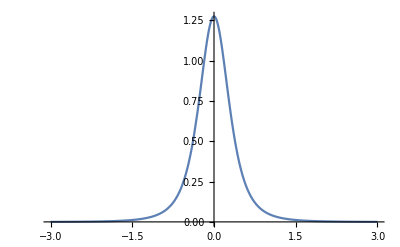

```mathematica
Plot[phat[0,1/2,0,y,1,0],{y,-3,3},PlotRange->Full]
```